```mathematica
n1=1;"$ player";
n2=1;"MG player";
n3=3;"Back ground";
n=n1+n2+n3;
m=2;
P=5;
T=399;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
nM=Table[0,{i,1,T}];
ΔcM=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
W=Table[190,{i,1,n}];
c=Table[100,{i,1,n}];
NStock=Table[9,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
Tinfor=Table[0,{i,1,P}];
Onetimes=Table[0,{i,1,P}];
CondionPinfor=Table[0,{i,1,P}];
BScollect=Table[0,{i,1,n}];
```

```mathematica
"initial set";
Do[
Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^P-1}],2,P]];
Do[Action⟦1,k⟧=(2*Action⟦1,k⟧-1),{k,1,P}];
RandomStrategy=Action;
AgentStrategy⟦i,s⟧=Flatten[RandomStrategy,1],{s,1,S},{i,1,n}]
```

```mathematica
AgentStrategy
```

{{{-1,-1,-1,1,-1},{-1,1,1,-1,1}},{{1,1,1,1,-1},{-1,1,1,1,-1}},{{1,-1,-1,1,1},{1,-1,1,-1,1}},{{1,1,1,-1,-1},{-1,1,1,1,1}},{{-1,1,-1,1,-1},{1,-1,1,1,-1}}}

```mathematica
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
```

```mathematica
BS
```

{{{-1,-1,-1,1,-1},0},{{-1,1,1,-1,1},0},{{1,-1,1,-1,1},0},{{1,1,1,-1,-1},0},{{-1,1,-1,1,-1},0}}

```mathematica
(Label[begin];
```

```mathematica
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
```

```mathematica
mu
t
```

{1,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

3

```mathematica
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];
Do[If[BS⟦i,1⟧==AgentStrategy⟦i,1⟧,BScollect⟦i⟧=BScollect⟦i⟧+1,BScollect⟦i⟧=BScollect⟦i⟧-1],{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
```

```mathematica
BS⟦All,1⟧
```

{{-1,-1,-1,1,-1},{-1,1,1,-1,1},{1,-1,-1,1,1},{1,1,1,-1,-1},{-1,1,-1,1,-1}}

```mathematica
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
nM⟦t⟧=(nM⟦t-1⟧+(-A⟦t-1⟧));
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
```

```mathematica
A
nM
```

{0,0,-1,-1,3,-1,-3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,1,2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,Do[c⟦i⟧=100,{i,1,n}];
Do[NStock⟦i,2⟧=9,{i,1,n}];Do[W⟦i⟧=190,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
W⟦i⟧=N[W⟦i⟧],{i,1,n}];];
ΔcM⟦t-1⟧=+A⟦t-1⟧*Price⟦t⟧;
```

```mathematica
Price
c
NStock
W
```

{10,10,10,10-1/(√5),10-2/(√5),10+1/(√5),10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{99.1056,79.1056,80.,139.106,100.}

{{10,9},{10,11},{10,11},{6,5},{10,9}}

{189.106,189.106,190.,189.106,190.}

```mathematica
Total[W]
```

947.317

```mathematica
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
```

```mathematica
PayoffFunction
U
```

{{-1,-1},{-1,1},{-1,1},{-1,1},{-1,-1}}

{{1,-1},{-5,-1},{-3,1},{3,5},{-3,1}}

```mathematica
t=t+1
```

7

```mathematica
"Go on or Stop";
If[t>T,Break,Goto[begin]];)//AbsoluteTiming
```

{2.99521,Null}

```mathematica
Tinfor
```

{55,47,47,52}

```mathematica
T
```

400

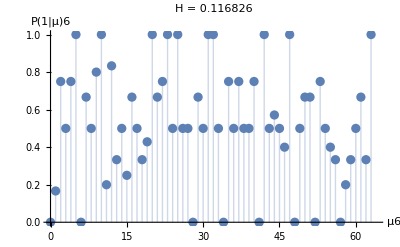

```mathematica
"P(1|μ4),P(1|μ6)";
Do[Tinfor⟦μ⟧=Tinfor⟦μ⟧+KroneckerDelta[mu⟦t⟧,μ-1];
Onetimes⟦μ⟧=Onetimes⟦μ⟧+UnitStep[A⟦t⟧]*KroneckerDelta[mu⟦t⟧,μ-1];,{t,Floor[T/2],T},{μ,1,P}];
"Tinfor";
Do[CondionPinfor⟦μ⟧=Onetimes⟦μ⟧/Tinfor⟦μ⟧,{μ,1,P}];
"prediction  H=Σ_(μ = 0)^(P - 1)ρ^μ<A|μ>^2,ρ^μ=T_μ/T";
Aonμ=0;
H=0;
Do[Do[Aonμ=Aonμ+A⟦t⟧*KroneckerDelta[mu⟦t⟧,μ-1],{t,Floor[T/2],T}];
Aonμ=Aonμ/Tinfor⟦μ⟧;
H=H+Tinfor⟦μ⟧/(T/2)*(Aonμ)^2;,{μ,1,P}]
f0=ListPlot[Table[{μ-1,CondionPinfor⟦μ⟧},{μ,1,P}],Filling
->Axis,PlotRange->{{0,P},{0,1}},AxesLabel-> {"μ"<>ToString[m],"P(1|μ)"<>ToString[m]},PlotLabel->"H = "<>ToString[N[H/n]]]
```

```mathematica
BScollect;
```

```mathematica
Q=1/n Sum[(2/T*BScollect⟦i⟧)^2,{i,1,n}]//N
```

0.438852

```mathematica
"Anylize   P(t+1)-P(t)=r(t)=(A (t))/λ   P(0)=10";
```

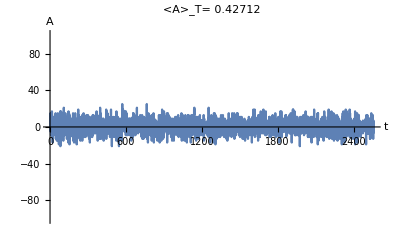

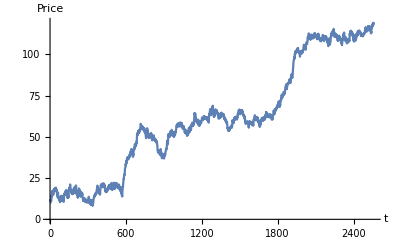

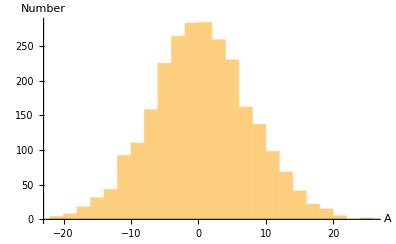

```mathematica
t1=0;
t2=T;
f1=ListPlot[A,AxesLabel->{"t","A"},PlotRange->{{t1,t2},{-n,n}},Joined->True,PlotLabel->"<A>_T= "<>ToString[N[Mean[A⟦t1+1;;t2⟧]]]]
f2=ListPlot[Price⟦t1+1;;t2⟧,AxesLabel->{"t","Price"},PlotRange->Automatic,Joined->True]
f3=Histogram[A⟦t1+1;;t2⟧,AxesLabel->{"A","Number"}]
```

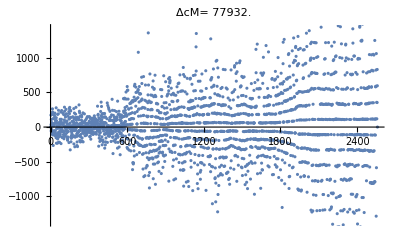

```mathematica
ListPlot[ΔcM,PlotLabel-> "ΔcM= "<>ToString[N[Total[ΔcM⟦3;;T⟧]]]]
```

```mathematica
nM
```

{0,0,0,1,-4,49,30,43,42,49,60,73,68,83,86,109,106,105,120,115,120,125,122,127,122,117,120,111,106,123,132,137,134,129,148,137,130,129,132,143,136,139,144,137,126,129,128,125,142,147,156,145,158,161,156,169,164,167,168,165,156,155,160,167,160,147,162,173,184,181,172,175,174,177,180,183,178,181,186,187,188,193,190,161,160,153,170,175,180,185,186,193,194,187,186,191,188,191,194,189,190,191,182,181,178,173,176,173,178,183,188,195,190,185,184,191,194,195,192,189,198,189,192,197,206,201,184,187,188,209,202,195,198,201,198,199,204,215,216,199,204,221,226,221,224,229,222,227,222,229,218,215,216,217,222,227,232,229,234,247,256,257,248,245,250,249,244,241,240,237,236,233,238,237,234,239,238,237,240,243,244,253,248,249,250,253,258,259,252,251,230,231,232,237,246,251,256,259,250,243,242,243,244,249,248,249,242,245,242,247,248,255,254,259,252,255,248,241,238,243,246,243,238,245,254,261,252,245,240,235,242,245,258,255,244,243,230,223,224,219,210,203,192,195,190,183,194,191,184,183,174,175,184,183,182,185,184,187,190,197,194,193,190,193,190,201,194,201,200,211,212,221,218,227,232,223,240,243,250,251,246,241,232,229,222,229,232,227,224,229,234,245,244,233,232,239,232,219,218,221,238,241,238,237,232,237,242,237,236,237,242,233,238,237,242,243,242,253,260,261,258,261,258,261,270,267,254,257,256,255,248,255,268,261,260,255,252,251,250,243,236,237,242,233,230,237,224,233,228,215,210,209,206,207,214,209,210,205,194,201,208,197,200,197,192,203,210,197,196,189,198,207,204,205,206,207,202,203,204,207,204,193,210,211,210,211,208,211,196,201,200,203,204,197,206,209,214,215,222,233,240,237,238,247,252,253,252,259,254,253,244,249,244,241,238,235,240,245,242,241,242,239,232,229,224,223,222,211,216,217,224,223,212,221,218,213,218,205,204,203,212,217,208,205,202,207,214,209,212,213,210,203,200,189,198,211,214,215,212,211,206,211,216,211,206,197,196,199,194,197,198,193,196,197,196,197,208,209,208,203,198,203,200,213,220,217,222,219,218,211,202,201,198,201,202,205,206,207,214,211,224,221,224,227,226,225,228,221,216,207,214,223,216,213,220,221,214,209,202,203,202,187,188,185,186,189,190,195,198,197,188,187,202,189,192,195,198,189,188,179,176,183,196,203,204,209,212,211,214,215,226,233,232,233,234,231,238,253,244,249,254,257,266,273,280,285,282,277,278,275,268,273,268,271,262,263,262,257,254,261,262,265,272,269,268,259,258,259,262,267,272,281,274,283,286,281,284,285,288,291,294,289,302,295,298,301,296,297,308,317,306,295,290,291,288,283,274,273,264,267,274,277,282,279,284,289,292,289,274,279,274,277,278,281,282,293,296,301,298,301,298,295,302,297,294,297,296,297,298,301,294,291,288,293,294,287,296,303,302,303,302,301,304,305,308,309,308,307,310,311,314,313,312,309,310,315,320,317,310,305,308,301,302,295,296,295,296,291,294,301,308,313,324,325,324,325,318,321,320,319,318,323,318,317,318,319,322,335,338,343,342,343,340,333,334,335,336,339,336,345,340,347,352,353,354,357,360,351,350,353,352,349,346,335,332,323,326,329,318,323,326,319,324,333,328,333,328,329,332,335,336,339,338,331,330,325,332,337,340,351,348,351,356,351,346,341,344,353,352,353,350,347,346,333,332,331,332,329,326,333,332,325,330,331,326,327,334,319,312,315,316,313,314,301,300,303,302,295,292,293,292,297,298,299,304,311,314,313,314,313,306,305,302,299,302,305,300,297,294,297,296,293,292,297,300,303,294,291,286,279,274,265,262,273,272,271,264,267,266,273,270,265,268,265,260,255,260,255,250,255,260,259,260,251,254,255,268,261,256,251,254,255,252,253,252,245,244,243,246,251,248,241,246,251,258,265,270,263,258,255,254,253,252,253,260,259,254,253,254,255,260,269,268,273,270,273,272,275,276,281,288,289,298,305,296,307,300,301,304,303,302,301,296,303,300,297,306,295,294,297,300,305,308,315,310,309,310,321,324,321,326,325,326,321,324,329,320,315,314,317,318,325,324,321,316,319,314,311,308,301,300,293,284,283,288,297,304,303,300,301,308,307,312,309,316,319,318,315,320,327,328,323,326,321,324,331,340,345,340,345,342,331,330,321,316,315,310,321,314,315,314,323,322,325,322,325,326,337,334,325,324,325,328,329,326,327,332,331,328,339,338,343,336,341,340,337,350,345,342,335,330,329,328,333,332,329,326,327,334,337,346,351,346,341,334,333,338,343,350,351,354,357,346,353,348,357,360,355,354,357,382,383,382,377,380,381,378,375,354,355,352,351,354,343,342,345,334,327,326,327,332,337,330,329,330,337,340,333,342,339,342,339,354,353,350,357,356,357,356,359,358,365,378,385,386,373,390,389,386,393,388,393,388,393,396,397,398,397,396,397,396,397,398,399,396,395,394,393,392,393,392,395,392,389,388,389,390,391,386,389,390,391,396,401,398,391,390,397,398,395,394,381,386,391,400,399,408,421,422,425,420,427,424,411,400,395,394,391,398,399,398,389,394,393,390,391,390,389,390,391,392,399,394,395,406,409,404,397,390,391,386,373,374,363,364,359,364,355,352,351,344,345,336,339,336,337,350,351,358,371,376,373,372,385,388,393,388,387,388,387,388,383,374,377,374,377,372,369,366,373,366,367,374,371,368,369,358,347,332,335,334,341,342,335,332,343,346,351,346,365,364,357,356,345,348,353,354,355,360,359,360,359,362,371,366,359,372,367,368,367,368,369,374,377,378,377,368,365,370,379,376,383,380,381,390,393,388,387,382,389,388,381,388,383,380,383,386,381,388,385,390,389,388,385,386,387,382,387,392,385,390,395,392,387,390,387,398,405,408,401,410,413,410,411,410,411,418,421,420,419,414,413,414,421,434,435,430,439,430,427,440,441,440,433,430,429,428,425,420,413,418,417,424,427,428,431,426,421,420,427,424,427,432,429,428,423,428,431,428,431,428,429,432,437,442,445,446,449,440,435,416,409,412,407,412,401,406,411,418,413,414,413,414,427,432,435,432,431,434,431,430,433,430,435,438,445,434,443,438,441,442,437,430,419,428,423,424,429,432,433,430,431,438,441,444,441,440,437,440,441,440,439,442,437,442,435,432,431,432,433,440,443,436,433,434,433,438,441,438,433,434,435,436,433,432,433,428,429,424,421,420,417,420,415,412,415,424,423,426,425,434,435,440,441,444,439,434,435,436,431,434,427,424,417,418,413,416,417,414,415,414,407,408,409,414,417,410,411,416,417,424,427,432,431,440,439,432,427,436,435,428,427,422,425,424,427,426,419,418,419,416,417,408,409,410,413,410,409,410,403,402,405,410,413,414,413,408,401,408,417,420,417,408,409,410,413,416,411,406,411,404,403,402,399,408,403,404,409,400,395,396,381,380,377,384,369,370,373,372,377,382,375,382,385,396,399,406,405,406,401,402,393,400,397,398,385,388,395,390,379,380,387,402,405,408,419,422,425,420,431,434,437,438,437,432,439,432,435,436,433,432,431,432,429,430,427,422,415,420,427,424,423,424,425,418,423,414,413,412,421,422,435,442,439,436,441,444,445,452,449,438,437,442,439,438,447,456,449,452,445,452,449,446,443,438,439,434,421,406,407,404,403,398,409,416,415,418,417,424,433,436,433,428,427,418,415,412,411,408,409,404,399,400,397,394,391,394,395,394,395,396,399,398,395,394,397,406,403,406,397,396,403,400,399,404,407,414,413,412,409,402,401,398,415,418,407,400,397,380,387,384,383,380,373,362,365,364,365,364,375,376,375,380,381,384,387,384,383,386,373,370,371,364,367,370,367,366,373,378,373,374,375,370,373,368,363,366,357,354,357,368,367,358,361,360,371,380,377,384,393,394,387,380,381,382,393,392,395,392,389,388,391,392,397,404,403,402,405,406,407,408,415,422,425,420,415,410,411,416,421,420,427,428,425,422,427,430,433,426,429,426,431,426,435,428,421,426,421,420,423,422,425,426,419,424,421,424,439,434,439,440,443,442,437,430,437,432,431,438,439,438,439,444,439,446,447,444,443,448,441,446,447,452,445,446,455,450,437,430,431,432,437,448,459,470,465,466,471,480,477,474,477,476,481,490,493,490,489,482,477,480,479,478,479,478,477,480,483,478,483,478,485,480,473,474,471,472,475,484,485,478,479,476,469,466,467,466,465,470,457,454,453,458,455,452,451,458,457,460,455,458,455,466,467,470,475,474,477,472,477,478,481,488,489,480,489,492,495,504,497,496,499,502,503,502,497,502,495,486,483,486,479,474,473,476,465,470,471,470,475,474,481,488,487,484,479,478,481,472,483,480,483,470,465,462,469,472,479,480,491,500,491,492,487,484,483,484,485,486,485,484,479,486,495,496,497,490,489,490,491,484,489,492,485,486,495,486,493,486,491,500,493,488,491,498,493,490,489,490,491,488,489,494,489,494,499,502,503,502,487,488,479,478,481,472,471,468,473,484,491,490,495,504,501,510,509,508,511,518,517,518,515,518,519,518,505,498,495,502,499,506,501,500,499,508,513,508,505,500,485,488,489,494,489,494,493,490,497,496,497,492,493,490,487,484,485,486,479,480,479,480,475,462,471,474,469,470,473,478,481,488,485,484,495,492,485,488,485,496,501,502,505,498,497,498,499,494,497,502,499,496,501,504,509,510,515,510,509,498,495,490,495,488,489,494,495,488,491,494,493,498,503,510,505,500,501,496,497,496,505,508,509,520,529,528,529,526,531,528,529,524,525,528,531,532,535,534,535,542,543,546,541,540,549,550,557,556,553,556,569,568,567,568,575,568,561,566,563,564,559,556,561,564,563,572,575,580,583,584,587,582,585,584,585,594,603,598,601,594,605,612,611,616,619,618,621,628,635,638,629,630,633,638,629,620,625,624,621,624,629,626,621,626,619,618,625,628,631,630,637,650,649,646,635,632,623,630,631,628,633,634,633,628,627,632,621,626,629,628,619,626,629,628,629,636,633,628,633,642,639,632,631,632,635,638,635,632,617,620,615,624,625,622,621,620,617,624,625,638,639,644,649,648,645,652,655,646,641,648,643,642,643,646,651,640,647,648,647,640,637,638,631,634,635,632,633,636,641,638,635,630,631,630,633,634,643,636,637,636,633,632,637,636,635,632,633,646,637,640,637,634,633,620,623,616,609,604,601,610,601,602,599,608,597,606,605,604,605,606,609,614,609,602,603,594,589,590,591,588,587,598,599,600,597,598,597,598,597,596,601,604,603,610,613,620,625,630,631,622,619,620,617,624,621,618,617,618,623,622,623,622,623,632,637,634,635,634,641,636,637,636,643,644,643,652,655,652,653,650,659,650,649,652,647,650,647,644,645,650,653,652,657,652,651,648,645,650,651,654,659,660,657,656,657,656,663,666,659,668,673,672,681,676,677,684,673,674,677,682,693,684,681,680,675,672,675,678,687,686,683,684,685,684,689,688,679,674,677,674,677,680,679,678,691,690,689,688,689,690,689,690,695,690,691,694,693,686,703,702,709,706,701,700,699,698,699,700,703,708,705,712,715,710,707,706,701,700,697,694,697,696,693,692,693,692,695,700,695,692,689,686,679,690,695,704,707,712,717,716,719,718,719,720,715,696,691,698,691,690,697,698,697,700,697,704,707,708,707,702,705,706,709,708,707,702,701,704,713,714}

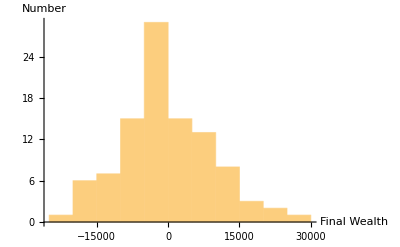

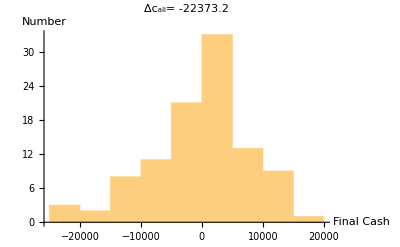

```mathematica
f4=Histogram[W⟦2;;n⟧-190,Automatic,AxesLabel->{"Final Wealth","Number"}]
f5=Histogram[c⟦1;;n⟧-100,Automatic,AxesLabel->{"Final Cash","Number"},PlotLabel-> "Δc_all= "<>ToString[N[Total[c⟦1;;n⟧-100]]]]
```

```mathematica
Sum[A⟦t⟧*Price⟦t⟧,{t,1,T}]//N
Sum[1/(√n)(A⟦t⟧)^2,{t,1,T}]//N
```

11221.4

5728.73

```mathematica
c
```

{-117.913,2742.89,-6467.88,507.166,-15793.9,-7877.01,2937.71,12886.8,16011.4,5602.37,-2623.22,13986.4,8147.35,-585.691,-15287.1,-10469.4,7017.31,11421.5,-3769.09,-1811.38,-15420.,-13.6204,-12353.,-4512.65,-15424.3,-1994.65,-12016.4,-13632.5,3716.09,10951.5,7743.28,7701.99,4525.05,4759.5,-12894.1,10824.7,-8774.24,13832.5,-12025.,22391.8,7784.61,7711.14,-1155.05,3723.66,-4565.58,5531.06,12931.2,12880.6,6209.06,-12902.7,-12179.5,65.8824,-8060.59,-6415.14,-11475.,14451.6,8774.72,-16664.1,1988.24,-7848.19,-7736.45,-5882.2,8294.03,702.29,4445.94,-12353.,-6144.4,-9079.44,-15455.4,11760.8,-7721.12,16191.8,-6664.5,-11517.2,-10866.5,22351.9,485.469,-6436.84,-6529.36,10912.,-6418.1,-3852.37,-11626.9,-5141.01,-1659.12,6960.28,4652.83,-9069.69,6844.47,14452.5,-16676.,-11381.2,-2028.88,-11958.1,507.166,-4742.42,-8723.7,-15356.6,-926.169,14451.6,14442.8}